ToDo:  
Figure out how to choose beta.  One idea is that we balance the contribution of the non-beta term with the beta term so that each contributes equally to the reward function (easy to do).  A more convincing method would be to find a point where the policy is halfway between the beta=0 and beta=large policies (not so easy).

Try to add new features and remove features.  This must be done after we settle on value for beta.  Use correlation matrix for states to determine best candidates for removal.

Eventually (after first iteration), need to figure out when random-help policy should be applied.  If we only choose optimal help based on current best guess, we may not explore parts of policy-space vs. state that need exploring.  As we increase the amount of data, the fraction of time we use the random policy should decrease.  We need some estimate of the probability that the second-best policy is, in fact, the best policy.

On logistic vs. step:  The distance of a point in feature space to the hyperplane has no meaning since we have not formulated a metric in that space.  Using a logistic function of the distance between point and the hyperplane (function linearPolicy) thus doesn't make much sense.  The Budinich paper uses the logistic but only as a numerical trick.  In our numerical experiments, the global fit routines performed much better than the gradient-based routines anyway so the main motivation for this numerical trick doesn't apply.  [Note that the whole discussion of choosing beta in the Budinich paper is nonsense anyway since it is equivalent to rescaling the equation for the hyperplane.]

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/BRETT-STUFF

### State

```mathematica
Dimensions[state=Import["state-uwplatt.csv"]]
```

{15327,10}

```mathematica
state[[1]]
```

{ttID,logSessionTime,fracSessionFlounderTime,logNowFlounderSteps,logNowFlounderTime,logNowStepTime,sessionCorrect,sessionIncorrect,sessionHelp,fracSessionCorrect}

Create hash table for fast lookup

```mathematica
Map[(state1[#[[1]]]=Rest[#])&,Rest[state]];
nFeatures=Length[Rest[state[[1]]]]
```

9

### Reward

```mathematica
Dimensions[reward=Import["reward-md5:e2ed3385.csv"]]
```

Import::nffil: File not found during Import.

{}

```mathematica
Dimensions[reward=Import["reward-uwplatt-2Y130.csv"]]
```

{812,12}

```mathematica
Dimensions[reward=Import["reward-uwplatt.csv"]]
```

{7210,12}

This must be reset any time a reward file is loaded :

```mathematica
Clear[rewardPosition];rewardPosition[x_]:=rewardPosition[x]=First[First[Position[reward[[1]],x,1,1]]];
rewardValue[x_,y_]:=x[[rewardPosition[y]]]
```

```mathematica
reward[[1]]
```

{KC,clientID,ttID,learning,slipTurns,slip,spontaneous-hint,no-hints,GIVE-BACKWARDS-HINTS,forwards-hint,zz-unclassified-hint,zz-extra-hint}

### Evaluate State & Reward

```mathematica
Map[Histogram[Rest[#],PlotLabel->First[#],PlotRange->All]&,Transpose[Map[Rest,state]]]
```

```mathematica
TableForm[Correlation[Map[Rest,Rest[state]]],TableHeadings->{Rest[state[[1]]],Rest[state[[1]]]}]
```

| logSessionTime | fracSessionFlounderTime | logNowFlounderSteps | logNowFlounderTime | logNowStepTime | sessionCorrect | sessionIncorrect | sessionHelp | fracSessionCorrect
logSessionTime | 1. | 0.651338 | 0.311562 | 0.301274 | 0.0736642 | 0.721848 | 0.642297 | 0.501846 | -0.417251
fracSessionFlounderTime | 0.651338 | 1. | -0.0575093 | -0.0696664 | -0.0705747 | 0.428488 | 0.477 | 0.32602 | -0.370403
logNowFlounderSteps | 0.311562 | -0.0575093 | 1. | 0.962906 | 0.0545284 | 0.0111198 | 0.26894 | 0.192042 | -0.476544
logNowFlounderTime | 0.301274 | -0.0696664 | 0.962906 | 1. | 0.109902 | 0.00164358 | 0.22699 | 0.139857 | -0.45948
logNowStepTime | 0.0736642 | -0.0705747 | 0.0545284 | 0.109902 | 1. | -0.0444632 | -0.0232201 | -0.150746 | -0.0172625
sessionCorrect | 0.721848 | 0.428488 | 0.0111198 | 0.00164358 | -0.0444632 | 1. | 0.661039 | 0.489532 | -0.0344468
sessionIncorrect | 0.642297 | 0.477 | 0.26894 | 0.22699 | -0.0232201 | 0.661039 | 1. | 0.397376 | -0.319528
sessionHelp | 0.501846 | 0.32602 | 0.192042 | 0.139857 | -0.150746 | 0.489532 | 0.397376 | 1. | -0.26693
fracSessionCorrect | -0.417251 | -0.370403 | -0.476544 | -0.45948 | -0.0172625 | -0.0344468 | -0.319528 | -0.26693 | 1.

List different policy combinations and number of instances of each

```mathematica
Block[{pp=Map[Drop[#,6]&,Rest[reward]]},Map[{#,Count[pp,#]}&,Union[pp]]]
```

{{{0,0,0,0,0,1},1},{{0,0,0,0,1,0},19},{{0,0,0,1,0,0},33},{{0,0,1,0,0,0},17},{{0,1,0,0,0,0},459},{{1,0,0,0,0,0},236},{{1,0,0,0,1,0},46}}

### Analyze routines

Policy choice is represented by a 0 or 1; -1 means policy doesn' t apply.  There is some nonsense in Budinich paper about -1 & 1 being preferred, but Eqn. (2) in paper is effectively the same for either convention.

```mathematica
policyVector[x_]:={Which[rewardValue[x,"no-hints"]==1,0,rewardValue[x,"spontaneous-hint"]==1,1,True,-1],
Which[rewardValue[x,"GIVE-BACKWARDS-HINTS"]==1,1,rewardValue[x,"forwards-hint"]==1,0,True,-1]};
policyVector[x_,y_]:=policyVector[x][[y]];
nPolicies=2;  (* Number of policies *)
comparePolicies[x_,y_]:=If[x===-1||y===-1,0,(x-y)^2] (* For policy to not apply, -1 must be explicit *);
invertPolicy[x_]:=If[x<0,x,1-x]
```

```mathematica
useStep=True; (* Choose between step function and a logistic *)
linearPolicy[state_,x_]:=Block[{a=Drop[x,-1],b=x[[-1]]},Block[{h=a.state+b  (* divide this by Sqrt[a.a] to get distance of state from hyperplane. *)},If[ useStep,(Sign[h]+1)/2,(Tanh[h/(2 Sqrt[a.a])]+1)/2]]]
```

Maybe should have weight for integrated probability (probability student has already learned skill before this step).

```mathematica
rewardFunctionTerm[beta_,x_,policy_,r_]:= 
Block[{pp=linearPolicy[state1[r[[3]]],x]},(r[[4]]+If[r[[5]]>0 ,beta (1-r[[6]])/r[[5]],0])comparePolicies[pp,policyVector[r,policy]]+If[r[[5]]>0,beta r[[6]]/r[[5]],0] comparePolicies[pp,invertPolicy[policyVector[r,policy]]]];
rewardFunction[beta_,x_]:=Sum[rewardFunction[beta,x[[i]],i],{i,nPolicies}];rewardFunction[beta_,x_,policy_]:=Apply[Plus,Map[rewardFunctionTerm[beta,x,policy,#]&,Rest[reward]]]
```

```mathematica
globalMinimum=True; (* Find global minimum or use gradient method for local *)
minimizer[fcn_,xx_,opts___]:=If[globalMinimum,NMinimize[fcn,xx,opts],FindMinimum[fcn,Map[{#,(Random[]-0.5)}&,xx],opts]];
minit[beta_,policy_,opts___]:=Block[{xx=Table[x[i],{i,nFeatures+If[useStep,0,1]}],zz,zzz,yy,yyy},
If[useStep,
(* Try each side of hyperplane and take best fit.  Use b=-1 or +1 as normalization. *)
yy=Append[xx,1];
zz=minimizer[rewardFunction[beta,yy,policy],xx,opts];
yyy=Append[xx,-1];
zzz=minimizer[rewardFunction[beta,yyy,policy],xx,opts];
	If[First[zzz]<First[zz],zz=zzz;yy=yyy],
(* For logistic, b is a fit parameter. *) 
yy=xx;zz=minimizer[rewardFunction[beta,yy,policy],xx,opts]];{First[zz],yy/.zz[[2]]}];
(* Add up the contribution from each policy to the reward function *)
minP[beta_,opts___]:=Block[{mp=Table[minit[beta,i,opts],{i,nPolicies}]},{Apply[Plus,Map[First,mp]],Map[#[[2]]&,mp]}]
```

Count, for each step where a policy choice can be made, number of instances of each policy choice or pair of policy choices.  If input is not a list, use original choice taken by Andes.

```mathematica
getPolicyVector[x_,r_]:=If[Head[x]===List,Map[linearPolicy[state1[r[[3]]],#]&,If[MatrixQ[x],x,Partition[x,nFeatures+1]]],policyVector[r]];
dist[x_]:=Block[{y=Map[getPolicyVector[x,#]&,Rest[reward]]},TableForm[Map[Count[y,#]&,Union[y]],TableHeadings->{Union[y],None}]];
dist[x_,y_]:=Block[{z=Map[{getPolicyVector[x,#],getPolicyVector[y,#]}&,Rest[reward]],hx,hy},hx=Union[Map[#[[1]]&,z]];hy=Union[Map[#[[2]]&,z]];TableForm[Outer[Count[z,{#1,#2}]&,hx,hy,1],TableHeadings->{hx,hy}]]
```

### Linear regression per choice

This is an idea suggested by Kurt.  For each policy choice, construct a linear model that predicts learning.

```mathematica
linearPolicyChoiceModels=Table[Block[{r=Select[Rest[reward],(policyVector[#][[policy]]==choice)&]},{choice,LinearModelFit[{Map[state1[#[[3]]]&,r],Map[#[[4]]&,r]}]}],{policy,nPolicies},{choice,0,1}];
```

```mathematica
choosePolicy[state_,policy_]:=Map[{#[[1]],#[[2]].state}&,linearPolicyChoiceModels[[policy]]]
```

### Analyze

Calculate random data point

```mathematica
rewardFunction[1.0,Table[(Random[]-0.5)*10,{nPolicies},{nFeatures+1}]]
```

34.6229

```mathematica
Block[{useStep=False},rewardFunction[1.0,Table[(Random[]-0.5)*10,{nPolicies},{nFeatures+1}]]]
```

38.9787

```mathematica
Timing[Block[{useStep=False},soln1=minP[1.0]]]
```

{41.4977,{16.3563,{{-5.44346,-66.2678,-56.5161,13.2849,10.5666,9.54659,-1.99712,6.17693,-54.1992,-43.9612},{18031.6,5838.28,-3518.26,5068.59,-4449.52,-3175.97,-947.967,457.496,-2767.03,-102207.}}}}

```mathematica
Timing[soln1=minP[1.0]]
```

{13.372,{27.3112,{{-1.60639,1.17417,1.69868,0.382953,1.14921,1.78659,-1.85259,-0.940264,-0.0832238,1},{0.262076,0.538741,-1.25687,0.673844,-0.45726,-0.779582,-0.864641,0.137188,0.528542,-1}}}}

```mathematica
dist[0]
```

{-1,-1} | 34
{-1,0} | 19
{-1,1} | 17
{0,-1} | 459
{1,-1} | 236
{1,0} | 46

```mathematica
dist[soln1[[2]]]
```

{0,0} | 560
{0,1} | 31
{1,0} | 217
{1,1} | 3

### Different values of beta (step)

#### Calculate solutions

```mathematica
Timing[soln[0]=minP[0,Method->"DifferentialEvolution"]]
```

{192.317,{42.0774,{{-1.44919,1.54353,4.87327,-1.09088,1.35604,0.734676,-0.468648,-0.147958,-0.0782796,-1},{-2.29899,-2.5238,0.40462,-5.95492,-1.89085,0.618451,-2.00407,1.19309,2.05663,1}}}}

```mathematica
Timing[soln[1/8]=minP[0.125,Method->"DifferentialEvolution"]]
```

{786.082,{63.1654,{{-1.07316,-1.13538,3.42854,-0.212579,1.05226,0.964525,-1.73238,0.503803,-1.16728,1},{-4.59316,3.06104,-6.87889,-1.93027,-10.326,1.97714,-2.27647,2.28313,-1.11761,1}}}}

```mathematica
Timing[soln[1/4]=minP[0.25,Method->"DifferentialEvolution"]]
```

{622.771,{83.3896,{{-0.305959,0.262831,1.19172,-1.68184,-3.60467,-0.563667,0.014358,2.33417,0.0861073,-1},{-0.340386,1.25541,4.86956,-1.43988,-0.18261,0.00317903,-1.28088,0.859847,-1.44507,1}}}}

```mathematica
Timing[soln[1/2]=minP[0.5,Method->"DifferentialEvolution"]]
```

{931.789,{122.524,{{0.786477,-0.0243636,-1.34402,-2.24316,-8.19376,-0.0644791,-0.0818221,3.09568,-4.34073,-1},{0.128837,0.633537,4.05941,0.409272,-0.307684,-0.158705,-4.7045,2.69567,0.812324,-1}}}}

```mathematica
Timing[soln[1]=minP[1.0,Method->"DifferentialEvolution"]]
```

{923.91,{201.777,{{-1.69966,3.04342,-0.575237,-1.67384,-8.75362,-3.00237,0.0327774,6.24537,-0.923679,1},{0.669279,-2.60431,5.79142,-1.39378,3.74254,-0.616071,-9.59717,7.94689,-1.07041,-1}}}}

```mathematica
Timing[soln[2]=minP[2.0,Method->"DifferentialEvolution"]]
```

{798.83,{359.667,{{-0.406774,2.77928,0.420785,-4.45825,-9.23496,-0.555358,0.0905911,4.30716,1.34178,1},{0.688038,3.10612,1.37922,1.86845,1.69674,-2.43595,-0.00691656,-0.281299,-2.26483,-1}}}}

```mathematica
Timing[soln[4]=minP[4.0,Method->"DifferentialEvolution"]]
```

{769.315,{669.343,{{-0.706392,0.0781502,2.30756,-0.373411,-2.94333,-0.891699,-0.0699901,1.6193,-3.53853,1},{0.211874,0.85613,1.23875,0.0176827,1.67161,-3.16033,0.347035,-0.200527,-0.356964,-1}}}}

```mathematica
betaList={0,1/8,1/4,1/2,1,2,4};
```

```mathematica
Save["soln-uwplatt.m",{soln,betaList}]
```

#### Analyze Solutions

```mathematica
Get["soln-uwplatt-2Y130.m"];
```

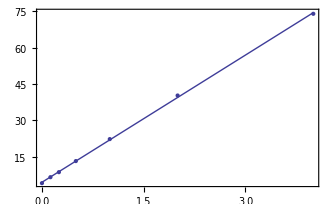

```mathematica
Block[{pp=Map[{#,First[soln[#]]}&,betaList],y},y=Fit[pp,{1,x},x];Show[ListPlot[pp,PlotRange->All,Axes->False,Frame->True],Plot[y,{x,0,4}]]]
```

```mathematica
Map[{#,soln[#][[1]],dist[soln[#][[2]]]}&,betaList]
```

{{0,4.03502,{0,0} | 651
{1,0} | 157
{1,1} | 3},{1/8,6.49599,{0,0} | 512
{0,1} | 110
{1,0} | 186
{1,1} | 3},{1/4,8.5747,{0,0} | 543
{0,1} | 107
{1,0} | 158
{1,1} | 3},{1/2,13.1504,{0,0} | 526
{0,1} | 100
{1,0} | 182
{1,1} | 3},{1,22.2159,{0,0} | 540
{0,1} | 81
{1,0} | 185
{1,1} | 5},{2,40.2047,{0,0} | 438
{0,1} | 197
{1,0} | 170
{1,1} | 6},{4,73.9173,{0,0} | 360
{0,1} | 292
{1,0} | 140
{1,1} | 19}}

Compare solutions for different beta values

```mathematica
Map[{#,dist[soln[0][[2]],soln[#][[2]]]}&,betaList]
```

{{0, | {0,0} | {1,0} | {1,1}
{0,0} | 651 | 0 | 0
{1,0} | 0 | 157 | 0
{1,1} | 0 | 0 | 3},{1/8, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 496 | 101 | 54 | 0
{1,0} | 16 | 9 | 132 | 0
{1,1} | 0 | 0 | 0 | 3},{1/4, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 528 | 100 | 23 | 0
{1,0} | 15 | 7 | 134 | 1
{1,1} | 0 | 0 | 1 | 2},{1/2, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 512 | 100 | 39 | 0
{1,0} | 14 | 0 | 142 | 1
{1,1} | 0 | 0 | 1 | 2},{1, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 528 | 78 | 45 | 0
{1,0} | 12 | 3 | 139 | 3
{1,1} | 0 | 0 | 1 | 2},{2, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 433 | 196 | 22 | 0
{1,0} | 5 | 1 | 147 | 4
{1,1} | 0 | 0 | 1 | 2},{4, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 354 | 289 | 4 | 4
{1,0} | 6 | 3 | 135 | 13
{1,1} | 0 | 0 | 1 | 2}}

### Try different methods (logistic)

Values for beta = 1.0, looks like NelderMead is fastest, although several methods find minimum.  It seems that minimum occurs for assumption that points are "far away" from the hyperplane in most methods.

```mathematica
Timing[Block[{useStep=False},soll["NelderMead"]=minP[1.0,Method->"NelderMead"]]]
```

{36.0085,{16.3563,{{-7.21134,-87.7897,-74.8709,17.5994,13.9983,12.6471,-2.64573,8.18302,-71.8016,-58.2385},{6.6533×10^18,2.15421×10^18,-1.29817×10^18,1.87021×10^18,-1.64179×10^18,-1.17187×10^18,-3.49781×10^17,1.68807×10^17,-1.02098×10^18,-3.77123×10^19}}}}

```mathematica
rewardFunction[1.0,soll["NelderMead"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False},soll["DifferentialEvolution"]=minP[1.0,Method->"DifferentialEvolution"]]]
```

{124.155,{16.3563,{{-894.738,-10892.4,-9289.51,2183.62,1736.83,1569.17,-328.265,1015.3,-8908.69,-7225.87},{3.86481×10^10,1.25135×10^10,-7.54088×10^9,1.08638×10^10,-9.5369×10^9,-6.80723×10^9,-2.03183×10^9,9.80576×10^8,-5.93073×10^9,-2.19066×10^11}}}}

```mathematica
rewardFunction[1.0,soll["DifferentialEvolution"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False},soll["SimulatedAnnealing"]=minP[1.0,Method->"SimulatedAnnealing"]]]
```

{37.7433,{16.3958,{{-300.413,604.133,-611.798,181.833,154.486,102.093,-21.4571,78.501,871.37,-206.964},{1.20866×10^6,391340.,-235829.,339748.,-298252.,-212885.,-63542.2,30666.,-185474.,-6.85093×10^6}}}}

```mathematica
rewardFunction[1.0,soll["SimulatedAnnealing"][[2]]]
```

26.7535

```mathematica
Timing[Block[{useStep=False},soll["RandomSearch"]=minP[1.0,Method->"RandomSearch"]]]
```

{460.248,{16.3563,{{-449171.,-5.46814×10^6,-4.66347×10^6,1.09621×10^6,871911.,787744.,-164794.,509694.,-4.47229×10^6,-3.62749×10^6},{181.921,58.9024,-35.4957,51.1371,-44.8912,-32.0424,-9.56404,4.61568,-27.9166,-1031.17}}}}

```mathematica
rewardFunction[1.0,soll["RandomSearch"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["ConjugateGradient"]=minP[1.0,Method->"ConjugateGradient"]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{7.41887,{16.4934,{{-0.117327,-0.724784,-0.444027,0.0582239,0.0865167,0.103864,-0.0209483,0.0653712,-0.69816,0.118356},{0.746417,4.35628,-0.644905,1.2699,-1.21268,-0.692358,-0.191049,0.157696,-1.73913,-3.62826}}}}

```mathematica
rewardFunction[1.0,soll["ConjugateGradient"][[2]]]
```

26.3575

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["PrincipalAxis"]=minP[1.0,Method->"PrincipalAxis"]]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0.12550865415375473`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {-0.06563686017330356`, -0.12550865415375473`, 0.1901308758732626`, « 4 », -0.3999405286388935`, 0.40978328093989036`, 0.39338889979834435`}.

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0.0583414738710753`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {0.602164570687847`, -0.0583414738710753`, 0.46632136103184874`, « 4 », -0.2600226969467423`, 0.17432140426394016`, 0.14905154772989582`}.

{42.9585,{16.3637,{{-1.13015,-17.206,-14.4187,3.38176,2.69917,2.40965,-0.509591,1.57351,-13.4752,-12.6217},{1.20229×10^13,3.8896×10^12,-2.34274×10^12,3.37744×10^12,-2.96611×10^12,-2.11753×10^12,-6.31984×10^11,3.04912×10^11,-1.84414×10^12,-6.81447×10^13}}}}

```mathematica
rewardFunction[1.0,soll["PrincipalAxis"][[2]]]
```

25.6779

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["Newton"]=minP[1.0,Method->"Newton"]]]
```

FindMinimum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{23.9064,{16.3563,{{-0.000921532,-0.0112186,-0.00956771,0.00224902,0.00178884,0.00161616,-0.000338096,0.0010457,-0.00917548,-0.00744227},{0.487405,0.157812,-0.0951008,0.137007,-0.120273,-0.0858485,-0.0256241,0.0123664,-0.0747946,-2.76272}}}}

```mathematica
rewardFunction[1.0,soll["Newton"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["QuasiNewton"]=minP[1.0,Method->"QuasiNewton"]]]
```

FindMinimum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{4.19636,{16.5817,{{-0.16525,-2.01173,-1.71569,0.403295,0.320776,0.289811,-0.0606276,0.187516,-1.64535,-1.33455},{2.90553×10^7,1.10566×10^7,5.41676×10^7,-9.9772×10^6,-5.97041×10^6,-3.46695×10^7,-792364.,658332.,-1.28151×10^7,-2.17306×10^7}}}}

```mathematica
rewardFunction[1.0,soll["QuasiNewton"][[2]]]
```

25.0931

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["InteriorPoint"]=minP[1.0,Method->"InteriorPoint"]]]
```

{29.2326,{16.3958,{{-0.00146663,0.00294941,-0.00298683,0.000887716,0.00075421,0.000498422,-0.000104755,0.000383245,0.00425407,-0.00101041},{0.0141712,0.00458837,-0.00276504,0.00398347,-0.00349693,-0.00249603,-0.000745018,0.000359551,-0.00217464,-0.0803256}}}}

```mathematica
rewardFunction[1.0,soll["InteriorPoint"][[2]]]
```

26.7535

### Try different methods (step)

Values for beta = 1.0, looks like DifferentialEvolution is the winner.  Also, the local (gradient-based) methods don't do so well, as expected.

```mathematica
Timing[minP[1.0,Method->"NelderMead"]]
```

{13.8299,{27.3112,{{-1.60639,1.17417,1.69868,0.382953,1.14921,1.78659,-1.85259,-0.940264,-0.0832238,1},{0.262076,0.538741,-1.25687,0.673844,-0.45726,-0.779582,-0.864641,0.137188,0.528542,-1}}}}

```mathematica
Timing[minP[1.0,Method->"DifferentialEvolution"]]
```

{73.9947,{22.2159,{{-2.22363,-0.51215,-0.597764,-0.658475,0.373787,1.55987,-0.70285,1.79517,0.7316,1},{2.77761,1.31107,8.47791,0.812072,-1.7461,-1.07446,-3.99113,-0.257346,-2.19814,1}}}}

```mathematica
Timing[minP[1.0,Method->"SimulatedAnnealing"]]
```

{12.0962,{26.4299,{{1.08148,0.402534,-0.882877,-0.670804,-1.16722,-0.00779751,-0.370066,-0.855371,-1.26073,1},{-0.317296,-1.92537,0.562287,2.06403,0.251333,-1.41328,-1.36115,1.40593,-0.410836,1}}}}

```mathematica
Timing[minP[1.0,Method->"RandomSearch"]]
```

{74.8576,{27.4779,{{0.607712,0.916715,-0.89115,-0.645028,-0.271974,0.184948,-0.335164,-0.291924,-0.46995,-1},{0.0226535,-0.480767,0.509769,-0.625674,-0.211372,-0.524167,0.00698119,0.0724676,-0.962017,1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"ConjugateGradient"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{0.898864,{34.0106,{{0.287277,0.228468,-0.0829359,-0.0232021,-0.472465,-0.0260645,-0.310585,-0.204015,0.163754,-1},{-0.391736,0.110272,0.15216,-0.417394,0.44709,-0.289161,0.364883,-0.145863,0.0300254,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"PrincipalAxis"]]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, -0.24787348721335978`, 0, 0, 0, 0, 0, 0, 0} from the point {0.23817887939121962`, 0.24787348721335978`, 0.4114634145391526`, « 3 », 0.303199830579842`, -0.42421225595153067`, 0.30643595262045453`}.

{6.93295,{28.1056,{{0.240305,0.173206,0.439959,0.274375,0.172664,0.375222,-0.373519,0.408029,0.381376,-1},{-1.91306,1.10103,-0.377832,0.273106,-1.21334,0.00941127,0.135983,0.334824,-6.68727,1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"Newton"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{1.91971,{29.5375,{{0.141128,-0.0568138,0.356574,0.136605,0.156504,0.0454842,-0.346532,0.0189378,-0.39294,-1},{-0.112677,-0.119968,0.361145,-0.266722,-0.194544,-0.36567,-0.279983,0.290092,-0.0511178,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"QuasiNewton"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{0.85687,{37.3532,{{-0.350285,0.248926,0.346871,0.277242,0.469966,-0.255852,-0.0404521,-0.10279,-0.391178,-1},{-0.0902049,0.286367,0.368838,0.0184495,-0.160944,0.288818,0.219123,0.269524,-0.00781578,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"InteriorPoint"]]]
```

{2.84157,{35.324,{{-0.488425,0.249156,0.0253755,-0.467364,0.114365,0.140335,0.0145052,0.378544,-0.148515,1},{0.399664,-0.114795,-0.0512132,0.489701,-0.478881,-0.46628,0.197257,0.195975,0.347784,-1}}}}

### Calculations for step model.

Expectation value for learning gain, 1-P(G)-P(s) in terms of: cbl = correct before learning, wbl = wrong before learning, cal = correct after learning, and wal = wrong after learning.  Not that there is a correction to the formula where we use the expectation values of P(G)=cbl/(cbl+wbl) and P(S)=wal/(cal+wal).

```mathematica
1-FullSimplify[Integrate[(g+s) g^cbl (1-g)^wbl s^wal (1-s)^cal,{g,0,1},{s,0,1},Assumptions->{cbl>-1,cal>-1,wal>-1,wbl>-1}]/(Integrate[g^cbl (1-g)^wbl,{g,0,1},Assumptions->{cbl>-1,wbl>-1}] Integrate[s^wal (1-s)^cal,{s,0,1},Assumptions->{cal>-1,wal>-1}])]
```

1-(1+wal)/(2+cal+wal)-(1+cbl)/(2+cbl+wbl)